## An undulator model with centrally symmetric

### here stores parameters that do not vary.

```mathematica
<<radia`;
initialRadia[]:=Block[{},
radUtiDelAll[];

br=1.24;mu={0.05,0.05};    (*Suscettivita'*)
matmag=radMatLin[mu,br];
matpole=RadMatAFK502[];

period=18.5;
poleDim={50,21,2.8};
magnetDim={64,26,period/2-poleDim[[3]]};
ear2D={5,5};
poleCut={0.2,3};
magnetCut={0.5,4};

Divpole={7(*+10*),6,3};
DivMag={4,4,4};
];
initialRadia[];
RadPlot3DOptions[];
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

### functions to build single pole and magnet

```mathematica
fpole[in_]:=Block[{p01,p02,p03,p04,p05,p06,p07,zshift,zangle,dimx,dimy,dimz,halfGap,dimXEar,dimYEar,cutZ,cutX},
{
{zshift,zangle},
{dimx(*half width*),dimy,dimz(*it's half-thickness*),dimXEar,dimYEar},
{halfGap},
{cutZ,cutX}
}=in;(*interpret the input*)

p01=radObjRecMag[{dimx/4,-dimy/2,dimz/4},{dimx/2,dimy,dimz/2},{0,0,0}];
p02=radObjCutMag[p01,{dimx/2-cutX,0,0},{1,1,0}][[1]];
p03=radObjCutMag[p02,{0,0,dimz/2-cutZ},{0,1,1}][[1]];
radObjDivMag[p03,Divpole];
p04=radObjRecMag[{dimx/2+ dimXEar/2,-dimy+ dimYEar/2,dimz/4},{dimXEar,dimYEar,dimz/2},{0,0,0}];
radObjDivMag[p04,{1,1,Divpole[[3 ]]}];
p05=radObjCnt[{p03,p04}];

p07=radTrfMlt[p05,radTrfPlSym[{0,0,0},{0,0,1}],2];
(*p07=radTrfMlt[p06,radTrfPlSym[{0,0,0},{1,0,0}],2];*)
radTrfOrnt[p07,radTrfTrsl[{0,-1*halfGap,0}]];
radMatApl[p07,matpole];
radObjDrwAtr[p07,{0.9,0.2,0.2}];
radTrfOrnt[p07,radTrfTrsl[{0,0,zshift}]];

p07
];

fmagnet[in_]:=Block[{p01,p02,p03,p04,p05,p051,p052,p06,p07,zshift,zangle,dimx,dimy,dimz,halfGap,cutZ,cutX,zReflect,mDirec},
{
{zshift,zangle},
{dimx(*half width*),dimy,dimz(*it's half-thickness*)},
{halfGap},
{cutZ,cutX},
mDirec
}=in;(*interpret the input*)

p01=radObjRecMag[{dimx/4,-dimy/2,0},{dimx/2,dimy,dimz},mDirec];
p02=radObjCutMag[p01,{dimx/2-cutX,0,0},{1,1,0}][[1]];
p03=radObjCutMag[p02,{0,0,dimz/2-cutZ},{0,1,1}][[1]];
p04=radObjCutMag[p03,{dimx/2-cutX,-dimy,0},{1,-1,0}][[1]];
p05=radObjCutMag[p04,{0,-dimy,dimz/2-cutZ},{0,-1,1}][[1]];
p051=radObjCutMag[p05,{0,-dimy,-(dimz/2-cutZ)},{0,-1,-1}][[1]];
p052=radObjCutMag[p051,{0,0,-(dimz/2-cutZ)},{0,1,-1}][[1]];
If[zshift==0,
p07=radObjCutMag[p052,{0,0,0},{0,0,-1}][[1]];radObjDivMag[p07,{DivMag[[1]],DivMag[[2]],DivMag[[3]]/2}],
p07=p052;radObjDivMag[p07,DivMag];];
radMatApl[p07,matmag];
radTrfOrnt[p07,radTrfTrsl[{0,-1*halfGap,0}]];
radObjDrwAtr[p07,{0.4,0.9,0.2}];
radTrfOrnt[p07,radTrfTrsl[{0,0,zshift}]];

p07
];
```

### functions for a planner hybrid undulator with termination

```mathematica
t00=AbsoluteTime[];

undulatorConstructor[in_]:=Block[{gap,undulator,termiAMagThickness,termiBMagThickness,termiPoleThickness,distPoleToMag,magACoordZ,endPoleCoordZ,magBCoordZ,mainMagnetArray,mainPoleArray,endMagnetBig,endMagnetSmall,endPole},
gap=in[[1]];

{
termiAMagThickness,
termiBMagThickness,
termiPoleThickness,
distPoleToMag
}=in[[2]];

magACoordZ=5.5*period/2+poleDim[[3]]/2+(termiAMagThickness/2);
endPoleCoordZ=magACoordZ+distPoleToMag+(termiPoleThickness+termiAMagThickness)/2;
magBCoordZ=endPoleCoordZ+distPoleToMag+(termiBMagThickness+termiPoleThickness)/2;
mainPoleArray=radObjCnt[fpole[#]&/@(Table[{{i*period/2+period/4,0},poleDim~Join~ear2D,{gap/2},poleCut},{i,0,5}])];
mainMagnetArray=radObjCnt[fmagnet[#]&/@(Table[{{i*period/2+0,0},magnetDim,{gap/2},magnetCut,{0,0,(-1)^i}},{i,0,5}])];

endMagnetBig=fmagnet[{
{magACoordZ,0},
magnetDim[[1;;2]]~Join~{termiAMagThickness},
{gap/2},
magnetCut,
{0,0,(-1)^6}}];

endPole=fpole[{
{endPoleCoordZ,0},
(poleDim[[1;;2]]~Join~{termiPoleThickness})~Join~ear2D,
{gap/2},
poleCut}];

endMagnetSmall=fmagnet[{
{magBCoordZ,0},
magnetDim[[1;;2]]~Join~{termiBMagThickness},
{gap/2},
{0.2,magnetCut[[2]]},
{0,0,(-1)^7}}];
undulator=radObjCnt[{mainMagnetArray,endMagnetBig,endMagnetSmall,mainPoleArray,endPole}];
RadTrfZerPara[#,{0,0,0},{0,0,1}]&@RadTrfZerPerp[#,{0,0,0},{1,0,0}]&@RadTrfZerPara[#,{0,0,0},{0,1,0}]&@undulator;
radTrfOrnt[undulator,radTrfRot[{0,0,0},{1,0,0},90 Degree]];(*to be compiliant with radFldPtcTrj[]*)
(*radTrfOrnt[undulator,radTrfTrsl[{100,0,0}]];*)
undulator];

undulator=undulatorConstructor[{4.2+0.1,{4.54,1.41,2.03,1.62}}];
(*{termiAMagThickness,termiBMagThickness,termiPoleThickness,distPoleToMag}*)
radObjDrw[undulator];
Show[Graphics3D[%]]
```

-Graphics3D-

### Solve

```mathematica
t0=AbsoluteTime[];
RadSolve[undulator,0.00001,10000];
Print["Solved in : ",AbsoluteTime[]-t0,"  seconds"];
```

Solved in : 26.426566  seconds

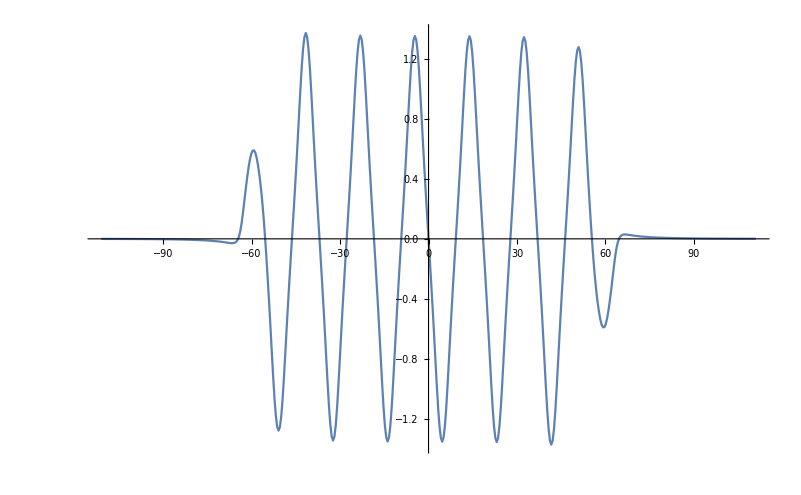

```mathematica
coord=Table[{0,i,0},{i,-period*6,period*6,period/40}];
b=radFld[undulator,"bz",#]&/@coord;
ListPlot[Transpose@{coord[[;;,2]],b},PlotRange->All,Joined->True]
```

```mathematica
coord01=Table[{0,i,0},{i,0,period*0.5,period/40}];
b01=radFld[undulator,"bz",#]&/@coord01;
b02=(b01[[;;-2]]~Join~Reverse[-b01])[[;;-2]];
Print["B_eff= ",2*Abs@Fourier[b02][[2]]/(√Length[b02])," T"];
Print["B_peak= ",Max[b02]," T"];
```

B_eff= 1.24381 T

B_peak= 1.35329 T

#### rolloff vs gap

```mathematica
rolloffCalc[{gap_,param_}]:=Block[{uForce,rolloff},
initialRadia[];
Print["gap= ",gap];
Divpole={7+10,5,3};
DivMag={4,4,4};

uForce=undulatorConstructor[{gap,param}];
RadSolve[uForce,0.00001,10000];

rolloff=Table[{x,-radFld[uForce,"Bz",{x,period/4,0}]},{x,-20,20,0.1}];

Transpose@{rolloff[[;;,1]],rolloff[[;;,2]]/Max[rolloff[[;;,2]]]-1}
];
```

```mathematica
param={4.54,1.41,2.03,1.62};
rgaps={4.2+0.1,6,20};
rolloffdata=rolloffCalc[{#,param}]&/@rgaps;
```

gap= 4.3

gap= 6

gap= 20

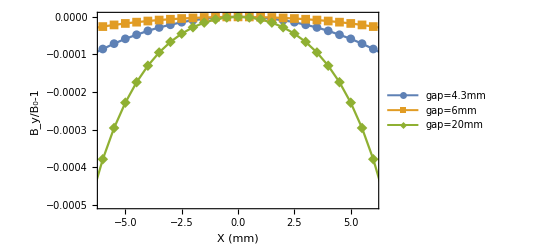

```mathematica
ListPlot[rolloffdata[[;;,;;;;5]],PlotRange->{{-6,6},{-0.0005,0.000002}},Mesh->All,ImageSize->Scaled[0.5],PlotMarkers->Automatic,FrameStyle->Directive[Black,Thickness[0.003],23],Joined->True,PlotRange->All,PlotStyle->Thickness[0.004],Frame->True,Axes->False,FrameLabel->{"X (mm)","B_y/B_0-1"},PlotLegends->Placed[{"gap=4.3mm","gap=6mm","gap=20mm"},{0.86,0.13}]]
```

```mathematica
rolloffCalc[{gap_,param_}]:=Block[{uForce,rolloff},
initialRadia[];
Print["gap= ",gap];
Divpole={7+10,5,3};
DivMag={4,4,4};

uForce=undulatorConstructor[{gap,param}];
RadSolve[uForce,0.00001,10000];

rolloff=Table[{x,-radFld[uForce,"Bz",{x,period/4,0}]},{x,-25,25,0.1}];

Transpose@{rolloff[[;;,1]],rolloff[[;;,2]]}
];
```

```mathematica
param={4.54,1.41,2.03,1.62};
rgaps={4.2+0.1};
rolloffdata=rolloffCalc[{#,param}]&/@rgaps;
```

gap= 4.3

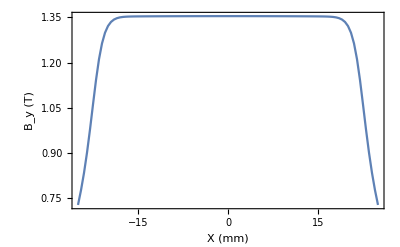

```mathematica
ListPlot[rolloffdata[[;;,;;;;5]],PlotRange->All,ImageSize->Scaled[0.5],Joined->True,FrameStyle->Directive[Black,Thickness[0.003],23],PlotRange->All,PlotStyle->Thickness[0.004],Frame->True,Axes->False,FrameLabel->{"X (mm)","B_y (T)"}]
```